```mathematica
Remove["Global`*"]
```

```mathematica
mat=Table[{Subscript[s1, i] Subscript[α, i],Subscript[s1, i] Subscript[β, i],Subscript[s2, i] Subscript[α, i],Subscript[s2, i] Subscript[β, i]},{i,4}];
(*mat=Table[{s1α[i],s1β[i],s2α[i],s2β[i]},{i,4}];*)
```

```mathematica
mat //MatrixForm
```

(s1 α_1 | s1 β_1 | s2 α_1 | s2 β_1
s1 α_2 | s1 β_2 | s2 α_2 | s2 β_2
s1 α_3 | s1 β_3 | s2 α_3 | s2 β_3
s1 α_4 | s1 β_4 | s2 α_4 | s2 β_4)

```mathematica
Det[mat] //FullSimplify
```

s2_2 (s1_3 s1_4 s2_1 (α_2 β_1-α_1 β_2) (α_4 β_3-α_3 β_4)+s1_1 (s1_4 s2_3 (α_3 β_2-α_2 β_3) (α_4 β_1-α_1 β_4)-s1_3 s2_4 (α_3 β_1-α_1 β_3) (α_4 β_2-α_2 β_4)))+s1_2 (-s1_4 s2_1 s2_3 (α_3 β_1-α_1 β_3) (α_4 β_2-α_2 β_4)+s2_4 (s1_3 s2_1 (α_3 β_2-α_2 β_3) (α_4 β_1-α_1 β_4)+s1_1 s2_3 (α_2 β_1-α_1 β_2) (α_4 β_3-α_3 β_4)))

```mathematica
u=A Exp[-α rp]+1 Exp[-β rp];
usq=Expand[u^2];
```

```mathematica
Integrate[(usq rp^2 Sin[θ])/Sqrt[(rp^2+r^2 - 2 rp r Cos[θ])],{rp,0,∞},{θ,0,π},Assumptions->{Re[α]>0&&Re[β]>0}]
```

$Aborted

```mathematica
func[r_]=Assuming[(Im[r]>0&&Im[r]+Re[r]≤0),Simplify[-2/r+integr[r]]];
text=Framed[Assuming[Re[α]>0&&Re[β]>0&&((Im[r]==0&&Re[r]<0)||(Im[r]<0&&Re[r]≤Im[r])||(Im[r]>0&&Im[r]+Re[r]≤0)),Simplify[PowerExpand[Simplify[PowerExpand[Simplify[func[r]]]]]]]]//TraditionalForm;
Print[Style[text,"Graphics",FontFamily->"Times"]]
Plot[{2/r+func[r]/.{α->.5,β->1.2,A->3,B->1},2/r+func[r]/.{α->1,β->1,A->1,B->1}},{r,-10,0},Frame->True,Axes->False,AspectRatio->Full,PlotTheme->"Detailed"] //Print
```

```mathematica
g=Series[Simplify[PowerExpand[Simplify[PowerExpand[Simplify[func[r]+2/r]]]]],{r,∞,0}]//Normal//PowerExpand//Expand//Simplify
```

(A^2 (8 ⅈ ⅇ^(-2 r α) π r^3-1/α^3)+B^2 (8 ⅈ ⅇ^(-2 r β) π r^3-1/β^3)+A B (16 ⅈ ⅇ^(-r (α+β)) π r^3-16/(α+β)^3))/(4 r)

```mathematica
√((g/.ⅈ->-ⅈ )*g)/.A->B/.α->β/.B->1/.β->1//PowerExpand//Simplify//Expand
```

-1/r+8 ⅈ ⅇ^(-2 r) π r^2

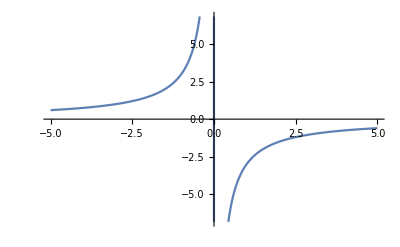

```mathematica
Plot[Re[%%%],{r,-5,5}]
```

```mathematica
integr[r]
```

ConditionalExpression[A^2 ⅇ^(-2 r α) r^2 Gamma[0,-2 r α]+1/4 (A^2/α^2+(2 A^2 r)/α+B^2/β^2+(2 B^2 r)/β+(8 A B)/(α+β)^2+(8 A B r)/(α+β)+4 B^2 ⅇ^(-2 r β) r^2 Gamma[0,-2 r β]+8 A B ⅇ^(-r (α+β)) r^2 Gamma[0,-r (α+β)]+4 A^2 ⅇ^(-2 r α) r^2 Log[-1/r]+4 B^2 ⅇ^(-2 r β) r^2 Log[-1/r]+8 A B ⅇ^(-r (α+β)) r^2 Log[-1/r]-4 A^2 ⅇ^(-2 r α) r^2 Log[α]+4 A^2 ⅇ^(-2 r α) r^2 Log[-r α]-4 B^2 ⅇ^(-2 r β) r^2 Log[β]+4 B^2 ⅇ^(-2 r β) r^2 Log[-r β]-8 A B ⅇ^(-r (α+β)) r^2 Log[α+β]+8 A B ⅇ^(-r (α+β)) r^2 Log[-r (α+β)]),Re[α]>0&&Re[β]>0&&((Im[r]==0&&Re[r]<0)||(Im[r]<0&&Re[r]≤Im[r])||(Im[r]>0&&Im[r]+Re[r]≤0))]